## Uniform Circular Motion

Motion of a circle at constant speed.

```mathematica
Animate[Graphics[{RGBColor[0,0,0,0],EdgeForm[Red],Disk[{0,0},1],RGBColor[1,0,0,1],Disk[{Cos[a],Sin[a]},0.05],Arrow[{{Cos[a],Sin[a]},{Cos[a]-0.5Sin[a],Sin[a]
+0.5Cos[a]}}]},PlotRange->1.1],{a,0,2π}]
```

Although the speed is constant, the object is accelerating because of the change in direction which affects the velocity.

## Centripetal Force and Acceleration

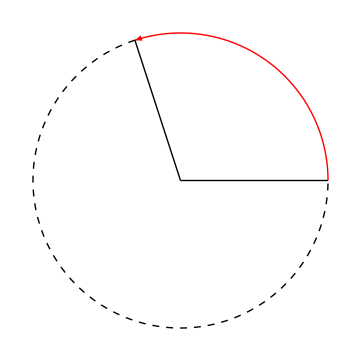

```mathematica
Graphics[{Red,Arrow[BezierCurve[{{Cos[#],Sin[#]}&/@Range[0,(3π)/5,π/360]}]],Black,Line[{{0,0},{1,0}}],Line[{{0,0},{Cos[(3π)/5],Sin[(3π)/5]}}],Dashed,BezierCurve[{{Cos[#],Sin[#]}&/@Range[(3π)/5,2π,π/360]}]}]
```